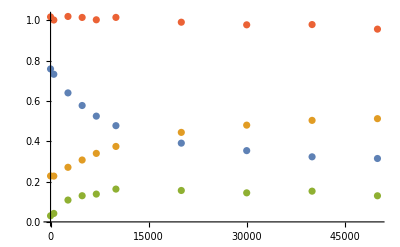

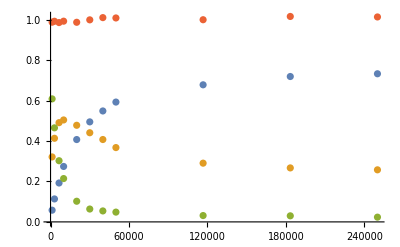

```mathematica
path="C:\\SC Lab\\GitHubRepositories\\Qubit-data-process\\PaperDataProcess\\Fluorescence shelving of a superconducting circuit\\Fluorescence\\";
file=path<>"average_population_measurements.hdf5";
data=Import[file, "Data"];
PumpingTime = data["/transient_time"];
TransientPopulationMatrix = data["/transient_population_matrix"];
DelayTime = data["/t1_time"];
T1PopulationMatrix = data["/t1_population_matrix"];


Population = Mean[Transpose[TransientPopulationMatrix, {3,2,1}]];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]


Population = Mean[Transpose[T1PopulationMatrix, {3,2,1}]];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{DelayTime,P0}];
P1toPlot=Transpose[{DelayTime,P1}];
P2toPlot=Transpose[{DelayTime,P2}];
PSumtoPlot=Transpose[{DelayTime,P0+P1+P2}];
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```